## 1. Фенотип.

```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\Studies\2 kurs\Neutral Networks\NG4P13 GolubovichRoman

```mathematica
Get["NG22P13Problem.mx","NG22P13"];
?Troubles
```

#### шаги

```mathematica
generateind[]:={RandomReal[{0,100}],
RandomReal[{0,100}],
RandomReal[{0,10}],
RandomReal[{0,360}]}
```

```mathematica
Troubles[{1,1,0,1}]
```

2.77303

```mathematica
inds= Table[{RandomReal[{0,100}],
RandomReal[{0,100}],
RandomReal[{0,10}],
RandomReal[{0,360}]},{i,100}];
```

```mathematica
PlotMarkers
```

```mathematica
indsRes = Troubles/@inds;
```

```mathematica
indsArrowEdges = {#[[1]]+#[[3]]*Cos[#[[4]] Degree],#[[2]]+#[[3]]*Sin[#[[4]]Degree]}&/@inds;
```

```mathematica
arrows = MapThread[Arrow[{#1,#2}]&,{inds[[;;,{1,2}]],indsArrowEdges}];
points = Point[#[[;;2]]]&/@inds;
```

```mathematica
inds= Table[{RandomReal[{0,100}],
RandomReal[{0,100}],
RandomReal[{0,10}],
RandomReal[{0,360}]},{i,300}];
```

```mathematica
indsres =Troubles/@inds;
```

```mathematica
inds[[Flatten@TakeSmallest[indsres->"Index",1]]]
```

{{91.8114,17.1259,3.13963,162.555}}

```mathematica
Cross
```

#### итог

```mathematica
generateind[]:={RandomReal[{0,100}],
RandomReal[{0,100}],
RandomReal[{0,10}],
RandomReal[{0,360}]}
```

```mathematica
ShowPhenotype[inds_]:=Block[{l = Length[inds],indsres = Troubles/@inds,indsArrowEdges,points = inds[[;;,{1,2}]],arrows, minindres,minind},indsArrowEdges ={#[[1]]+#[[3]]*Cos[#[[4]] Degree],#[[2]]+#[[3]]*Sin[#[[4]]Degree]}&/@inds;
arrows = MapThread[Arrow[{#1,#2}]&,{points,indsArrowEdges}];
minind=First@inds[[TakeSmallest[indsres->"Index",1]]];
minindres=First@TakeSmallest[indsres,1];
Graphics[{Lighter@ColorData["GreenPinkTones",indsres[[#]]],{AbsolutePointSize[4],Point@points[[#]],
Arrowheads[Small], arrows[[#]]}}&/@Range[l],Epilog->{Red,AbsolutePointSize@6,Point[minind[[{1,2}]]]},Axes->True,PlotRange->{{-10,110},{-10,110}},GridLines->Automatic,Frame->True,PlotLabel->Row[{ Style["Min",Red],":",StringForm["``→``",minind, minindres]}]]]
```

```mathematica
inds= Table[{RandomReal[{0,100}],
RandomReal[{0,100}],
RandomReal[{0,10}],
RandomReal[{0,360}]},{i,300}];
```

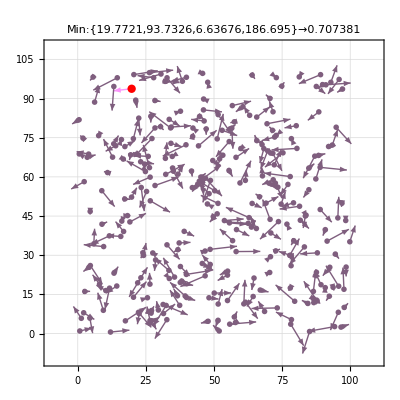

```mathematica
ShowPhenotype[inds]
```

### не то, но нашел нормальные точки

```mathematica
generateind[]:={RandomReal[{0,100}],
RandomReal[{0,100}],
RandomReal[{0,10}],
RandomReal[{0,360}]}
```

```mathematica
GenerateGoodPoints[L_,cond_:1]:=Block[{inds = Table[generateind[],{i,L}],addind, addindres},inds = inds[[Flatten@Position[Troubles/@inds,x_/;x<cond]]];
While[L>=Length@inds,addind = generateind[];addindres = Troubles[addind];If[addindres< 1,AppendTo[inds,addind]]];inds]
```

```mathematica
goodinds = GenerateGoodPoints[100,1];
```

```mathematica
ShowPhenotype[goodinds]
```

## 2. Квантование.

```mathematica
Length[IntegerDigits[360,2]]
```

9

для 10 4 бита
для 100 7 бит
для 360 9 бит

```mathematica
ClearAll[AnalogToDigital,DigitalToAnalog];
AnalogToDigital[{from_,to_},bits_Integer]:= IntegerString[Floor[(2^bits-1)*(#-from)/(to-from)],2]&;
DigitalToAnalog[{from_,to_},bits_Integer]:=Ceiling[from+FromDigits[#,2]*(to-from)/(2^bits-1)]&;
```

```mathematica
tmp = AnalogToDigital[{0,100},7][89]
```

1110001

Этот блок тестов лучше не запускать, потому что я поменял функцию DigitalToAnalog(добавил Ceiling), чтобы подать это в ToGray. Поэтому результаты тестов буду другие

```mathematica
(*Table[{i,Max[Abs[#-DigitalToAnalog[{0,100},i][AnalogToDigital[{0,100},i][#]]]&/@Range[0,100,0.1]]},{i,5,15}]*)
```

{{5,3.22258},{6,1.58571},{7,0.786614},{8,0.390196},{9,0.195499},{10,0.097654},{11,0.0488031},{12,0.0242979},{13,0.0121963},{14,0.00609778},{15,0.0030488}}

Для 100 достаточно брать 10 бит чтоб разница была максимум 0.1

```mathematica
(*Table[{i,Max[Abs[#-DigitalToAnalog[{0,10},i][AnalogToDigital[{0,10},i][#]]]&/@Range[0,10,0.01]]},{i,5,15}]*)
```

{{5,0.322258},{6,0.158571},{7,0.0786614},{8,0.0390196},{9,0.0195499},{10,0.0097654},{11,0.00488031},{12,0.00242979},{13,0.00121963},{14,0.000609778},{15,0.00030488}}

Для 10 также достаточно брать 10 бит чтоб разница была максимум 0.01

```mathematica
(*Table[{i,Max[Abs[#-DigitalToAnalog[{0,360},i][AnalogToDigital[{0,360},i][#]]]&/@Range[0,360]]},{i,5,15}]*)
```

{{5,11.5806},{6,5.57143},{7,2.82677},{8,1.35294},{9,0.702544},{10,0.348974},{11,0.175379},{12,0.0769231},{13,0.0438286},{14,0.0217909},{15,0.0109561}}

Для 360 также достаточно брать 9 бит чтоб разница была максимум 1. Для дальнейшей простоты дальше будем брать не 9, а 10

## 3. Код Грея.

```mathematica
ClearAll[ToGray,FromGray];
```

```mathematica
ToGray[n_Integer]:=IntegerString[BitXor[n,BitShiftRight[n]],2];
ToGray[n_Integer,len_Integer]:=IntegerString[BitXor[n,BitShiftRight[n]],2,len];
FromGray[g_String]:=Block[{gg=FromDigits[g,2],b},For[b=0,gg>0,,b=BitXor[b,gg];gg=BitShiftRight[gg,1]];
b]
```

```mathematica
ToGray[45]
```

111011

```mathematica
ToGray[45,10]
```

0000111011

```mathematica
(#==FromGray[ToGray[#]])&/@Range[100]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

## 4. Генетическое кодирование.

```mathematica
ClearAll[PhenotypeToGenotype,GenotypeToPhenotype];
PhenotypeToGenotype[{x_,y_,F_,α_}]:= Block[{xx = ToGray[DigitalToAnalog[{0,100},10][AnalogToDigital[{0,100},10][x]],10],
yy = ToGray[DigitalToAnalog[{0,100},10][AnalogToDigital[{0,100},10][y]],10],
FF = ToGray[DigitalToAnalog[{0,100},10][AnalogToDigital[{0,100},10][F]],10],
αα = ToGray[DigitalToAnalog[{0,100},10][AnalogToDigital[{0,100},10][α]],10]},
xx<>yy<>FF<>αα];
GenotypeToPhenotype[chromosome_String]:= Block[{lst = StringPartition[chromosome,10]},FromGray/@lst];
```

```mathematica
StringLength[tmp =PhenotypeToGenotype[{56,23,6,249}]]
```

40

```mathematica
GenotypeToPhenotype[tmp]
```

{56,23,6,249}

## 5. Популяция.

```mathematica
population20 = Table[generateind[],{i,20}];
```

```mathematica
StringSplit[PhenotypeToGenotype[population20[[1]]],""]
```

{0,0,0,1,1,0,1,0,1,0,0,0,0,0,0,0,1,1,1,1,0,0,0,0,0,0,0,1,1,0,0,1,1,0,0,0,0,0,0,1}

```mathematica
tmp = StringSplit[PhenotypeToGenotype[#],""]&/@population20;
```

```mathematica
asd2 = ToExpression//@tmp;
```

```mathematica
gens = PhenotypeToGenotype/@population20;
```

```mathematica
ShowGenotype[genotypes_]:=MatrixPlot[ToExpression//@(StringSplit[#,""]&/@genotypes),ColorFunction->"Monochrome"]
```

```mathematica
ShowGenotype[gens]
```

-Graphics-

видимо я взял всё-таки взял слишком много бит, потому что есть белые полосы, поэтому возьму меньше

```mathematica
ClearAll[PhenotypeToGenotype,GenotypeToPhenotype];
PhenotypeToGenotype[{x_,y_,F_,α_}]:= Block[{
xx = ToGray[DigitalToAnalog[{0,100},7][AnalogToDigital[{0,100},7][x]],7],
yy = ToGray[DigitalToAnalog[{0,100},7][AnalogToDigital[{0,100},7][y]],7],
FF = ToGray[DigitalToAnalog[{0,100},4][AnalogToDigital[{0,100},4][F]],4],
αα = ToGray[DigitalToAnalog[{0,100},9][AnalogToDigital[{0,100},9][α]],9]},
xx<>yy<>FF<>αα];
GenotypeToPhenotype[chromosome_String]:= Block[{lst = TakeList[ToExpression/@StringSplit[chromosome,""],{7,7,4,9}]},FromGray/@(StringJoin[ToString/@#]&/@lst)];
```

```mathematica
population20 = Table[generateind[],{i,20}];
```

```mathematica
gens = PhenotypeToGenotype/@population20;
```

```mathematica
StringLength@gens[[1]]
```

27

```mathematica
ShowGenotype[gens]
```

-Graphics-

## 6. Мутация.

```mathematica
ChangeBit[str_,pos_]:=ToString[If[ToExpression[StringTake[str,{pos}]]==1,0,1]]
```

```mathematica
gens[[1]]
```

0001100110000011001000000001000010100011

```mathematica
mut = RandomInteger[{1,StringLength[gens⟦1⟧]}]
```

8

```mathematica
ChangeBit[gens[[1]],mut]
```

0

```mathematica
ClearAll[GenOper]
GenOper["Mutation",individual_]:=Block[{mutGen=gens⟦individual⟧,pos=RandomInteger[{1,StringLength[gens⟦individual⟧]}]},gens⟦individual⟧=StringReplacePart[mutGen, ChangeBit[mutGen,pos],{pos,pos}];population20⟦individual⟧=GenotypeToPhenotype[gens⟦individual⟧]];
```

```mathematica
GenOper["Mutation",1]
```

{20,77,10,260}

```mathematica
Dynamic@ShowPhenotype[population20]
```

```mathematica
ClearAll[GenOper]
GenOper["Inversion",individual_]:=Block[{mutGen=gens⟦individual⟧},gens⟦individual⟧=StringReverse[gens[[individual]]];population20⟦individual⟧=GenotypeToPhenotype[gens⟦individual⟧]];
```

```mathematica
GenOper["Inversion",1]
```

{20,77,10,260}

```mathematica
Dynamic@ShowPhenotype[population20]
```

## 8. Скрещивание.

```mathematica
ClearAll[GenOper]
GenOper["Crossover",{parent1_,parent2_}]:=Block[{res=""},For[i=1,i<=StringLength@gens[[parent1]],i++,res = res<>If[RandomReal[]>0.5,StringTake[gens[[parent1]],{i}],StringTake[gens[[parent2]],{i}]]];
AppendTo[gens,res];AppendTo[population20,GenotypeToPhenotype[res]];];
```

```mathematica
GenOper["Crossover",{10,6}]
```

```mathematica
Dynamic@ShowPhenotype[population20]
```